```mathematica
Begin["BoatContext`"];
libboatLocation="/home/wolf/qea/libboat.nb";
libboat=NotebookOpen[libboatLocation];
SelectionMove[libboat,All,Notebook];
SelectionEvaluate[libboat];
Needs["CUDALink`"];
```

```mathematica
bHullLocation="/home/wolf/qea/bhull.stl";
hullLocation="/home/wolf/qea/hull.stl";

bHullLocation="/home/wolf/qea/boatfixed.stl";
hullLocation="/home/wolf/qea/boatfixed.stl";

(* Convert from STL file units to cm *)
stlUnits="Meters";
stlScale=QuantityMagnitude[UnitConvert[stlUnits,Quantity[, "Centimeters"]]];

(* Generate point cloud *)
bouyHullNonScaled=Import[bHullLocation,"BoundaryMeshRegion"];
bouyHull=TransformedRegion[bouyHullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*bouyHull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
bouyHullVolume=Volume[bouyHull]Quantity[, ("Centimeters")^3];
bouyHullPoints=pointCloud[bouyHull,100000];

hullNonScaled=Import[hullLocation,"BoundaryMeshRegion"];
hull=TransformedRegion[hullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*hull=Import["/home/wolf/qea/hulls/cube/cube.stl","BoundaryMeshRegion"];*)
hullVolume=Volume[bouyHull]Quantity[, ("Centimeters")^3];
hullCentroid=RegionCentroid[hull];

(* Constants *)
(*GeogravityModelData[CityData[Entity["City",{"Needham","Massachusetts","UnitedStates"}],"Coordinates"],"Magnitude"];*)
g=9.81 Quantity[, ("Meters")/("Seconds")^2];
blueFoamDensity=0.0317 Quantity[, ("Grams")/("Centimeters")^3];
waterDensity=1 Quantity[, ("Grams")/("Centimeters")^3];
```

```mathematica
hull
RegionCentroid[hullNonScaled]
```

-Graphics3D-

{-9.56012×10^-6,0.032645,0.16678}

```mathematica
can1Loc={0,0,-1};
can2Loc={0,0,1};
frontVec=Normalize[{0,1,0}];
boat={
<|
name->"BouyHull",
type->"Bouy",
mass->bouyHullVolume*waterDensity,
volume->bouyHullVolume,
points->bouyHullPoints,
front->frontVec,
render->{GraphicsComplex[MeshCoordinates@bouyHull,MeshCells[bouyHull,2]]},
cobRender->({White,PointSize[Large],Point[#]}&)
|>,
<|
name->"Hull",
type->"PointMass",
mass->hullVolume*blueFoamDensity,
volume->hullVolume,
com->Quantity[hullCentroid,"Centimeters"],
render->{
{Black,PointSize[Large],Point[hullCentroid]},
{EdgeForm[],Opacity[.6],LightPink,GraphicsComplex[MeshCoordinates@hull,MeshCells[hull,2]]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
volume->Quantity[, "USSodaCanVolumes"],
com->Quantity[can1Loc,"Centimeters"],
render->{Brown,PointSize[Large],Point[can1Loc]}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
volume->Quantity[, "USSodaCanVolumes"],
com->Quantity[can2Loc,"Centimeters"],
render->{LightBrown,PointSize[Large],Point[can2Loc]}
|>
};
```

```mathematica
UnitConvert[hullVolume,Quantity[, ("Centimeters")^3]]^(1/3)
```

10.5317 cm

```mathematica
calculateWaterLine[boat,Normalize[{0,1,1}]]
```

0.0424768

```mathematica
Manipulate[(
wNormal=Normalize[{Sin[θ],Cos[θ],0}];
renderBoatWithForces[boat,wNormal]),
{θ,0,Pi/2}]
```

Quantity::compat: Grams and Newtons are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

Part::pkspec1: The expression Floor[((85.6063) (779.+blueFoamDensity (1168.14)))/waterDensity] cannot be used as a part specification.

Quantity::compat: Grams and Newtons are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

Part::pkspec1: The expression Floor[((85.6063) (779.+blueFoamDensity (1168.14)))/waterDensity] cannot be used as a part specification.

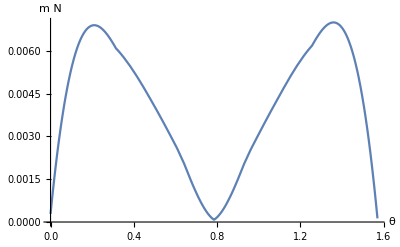

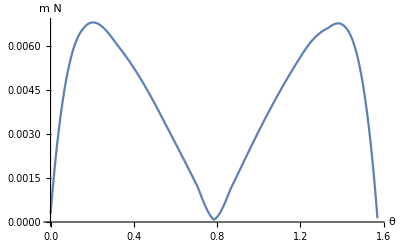

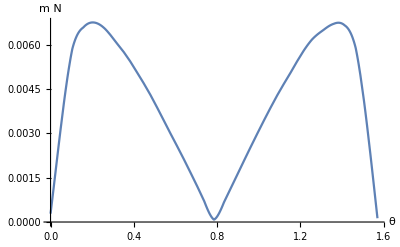

```mathematica
plotAVSMoments[boat,10]
plotAVSMoments[boat,20]
plotAVSMoments[boat,30]
```

```mathematica
DistributeDefinitions["BoatContext`"];
stuff=Parallelize[Table[
renderBoat[boat,Normalize[{Cos[θ],0,Sin[θ]}]],
{θ,0,Pi/2,(Pi/2)/100}
]];
```

```mathematica
DistributeDefinitions["BoatContext`"];
moments=Parallelize[Table[
calculateMoments[boat,Normalize[{Cos[θ],0,Sin[θ]}]],
{θ,0,Pi/2,(Pi/2)/100}
]];
```

```mathematica
mFunc=ListInterpolation[Table[Norm[Plus@@moments[[n]]],{n,Length[moments]}],{0,Pi/2}]
```

InterpolatingFunction[{{0., 1.5708}}, <>]

```mathematica
Manipulate[mFunc[θ],{θ,0,Pi/2}]
```

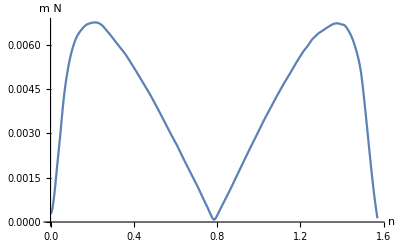

```mathematica
Plot[UnitConvert[mFunc[n],"NewtonMeters"],{n,0,Pi/2},AxesLabel->Automatic]
```

```mathematica
Interpolation[
Table[
Norm[Plus@@calculateMoments[boat,Normalize[{Cos[θ],0,Sin[θ]}]]],
{θ,0,Pi/2,(Pi/2)/10}
]
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

ListPlot::nonopt: Options expected (instead of {θ,0,π/2,π/20}) beyond position 1 in ListPlot[√(Abs[{«3»}×Quantity[«2»]+Quantity[0.,Times[«3»]]+Power[«2»] Cos[«1»] Quantity[«2»]]^2+Abs[{«3»}×Quantity[«2»]+Quantity[«1»]+Power[«2»] Quantity[«2»] Sin[«1»]]^2+Abs[{«3»}×Quantity[«2»]+Power[«2»] Cos[«1»] Quantity[«2»]+Power[«2»] Quantity[«2»] Sin[«1»]]^2),{θ,0,π/2,π/20}]. An option must be a rule or a list of rules.

ListPlot[√(Abs[{(Cos[θ] (310.977 g m/s^2))/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2)),0. g m/s^2,((310.977 g m/s^2) Sin[θ])/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))}×(Indeterminate cm)+0. g cm^2/s^2+(Cos[θ] (3.5354×10^-12 g cm^2/s^2))/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))]^2+Abs[{(Cos[θ] (310.977 g m/s^2))/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2)),0. g m/s^2,((310.977 g m/s^2) Sin[θ])/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))}×(Indeterminate cm)+0. g cm^2/s^2+((-3.5354×10^-16 g m^2/s^2) Sin[θ])/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))]^2+Abs[{(Cos[θ] (310.977 g m/s^2))/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2)),0. g m/s^2,((310.977 g m/s^2) Sin[θ])/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))}×(Indeterminate cm)+(Cos[θ] (0. g cm^2/s^2))/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))+((3.5354×10^-16 g m^2/s^2) Sin[θ])/(√(Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))]^2),{θ,0,π/2,π/20}]

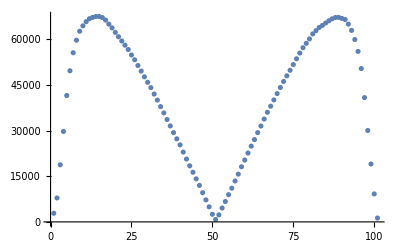

```mathematica
ListPlot[Table[Norm[Plus@@moments[[n]]],{n,1,Length[moments]}]]
```

```mathematica
stuff
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}